```mathematica
L=π+0.1;
κ=1;β=1;
γ1=2;γ2=0.5;
A1=0.1;B1=0.05;
```

```mathematica
tmax=500;
```

```mathematica
sol=NDSolve[{
D[u[x,t],t]==D[u[x,t],{x,2}]+u[x,t](1-u[x,t]-γ1 v[x,t]),
D[v[x,t],t]==κ D[v[x,t],{x,2}]+β v[x,t](1-v[x,t]-γ2 u[x,t]),
u[0,t]==0, u[L,t]==0,v[0,t]==0,v[L,t]==0,
u[x,0]==A1*Sin[π x/L],v[x,0]==B1*Sin[π x/L]},
{u,v},
{x,0,L},
{t,0,tmax}]
```

{{u→InterpolatingFunction[…],v→InterpolatingFunction[…]}}

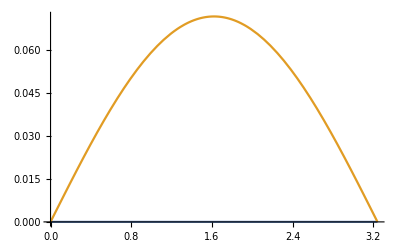

```mathematica
Plot[{Evaluate[u[x,tmax]/.sol],Evaluate[v[x,tmax]/.sol]},{x,0,L}]
```

```mathematica
xPoints=Range[0,L,L/100];
uPoints=Evaluate[u[xPoints,tmax]/.sol][[1]];
vPoints=Evaluate[v[xPoints,tmax]/.sol][[1]];
```

```mathematica
uvPoints={N[xPoints],uPoints,vPoints};
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(*Export["./spatial-competitive-lotka-volterra-2-3.csv",uvPoints]*)
```